```mathematica
ClearAll["Global`*"]
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/data/ppmr_fit_table.csv"}],"csv"];
```

```mathematica
ppmrfitdata
```

{{Fit,FitLow,FitHigh},{3.80806,3.64774,3.96838},{0.194142,0.169418,0.218866}}

```mathematica
ppmrfitdata[[2,1]]
ppmrfitdata[[3,1]]
```

3.80806

0.194142

```mathematica
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+bP+ξ)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->f*bP[M]};(*take σ*(1-R/k)=0 to take out starvation component*)
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R))+ρ)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->f*bP[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[3]]
Rsol = R/.LVSS[[3]]
```

-((α Y[M] (kRes (4 (ξ+f bP[M]-λ[M]+μ[M])^2 (ξ+f bP[M]+μ[M]+Y[M] ρ[M])+2 (5 f^2 bP[M]^2+2 λ[M]^2-5 λ[M] (ξ+μ[M])+(ξ+μ[M]) (5 (ξ+μ[M])+2 Y[M] ρ[M])+f bP[M] (-5 λ[M]+10 (ξ+μ[M])+2 Y[M] ρ[M])) σ[M]+(6 f bP[M]-2 λ[M]+6 (ξ+μ[M])+3 Y[M] ρ[M]) σ[M]^2)+2 ξ^2 √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+4 f ξ bP[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+2 f^2 bP[M]^2 √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))-2 ξ λ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))-2 f bP[M] λ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+4 ξ μ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+4 f bP[M] μ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] μ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M]^2 √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+2 ξ Y[M] ρ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+2 f bP[M] Y[M] ρ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))-2 Y[M] λ[M] ρ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+2 Y[M] μ[M] ρ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+2 ξ σ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+2 f bP[M] σ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] σ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M] σ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))-Y[M] ρ[M] σ[M] √(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2))))/(4 σ[M]^2 (2 (λ[M]+Y[M] ρ[M]) (ξ+f bP[M]+μ[M]+Y[M] ρ[M])+(2 λ[M]+3 Y[M] ρ[M]) σ[M])))

(kRes (2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])+√(kRes^2 (8 σ[M] (ξ+f bP[M]+μ[M]+σ[M])+(2 (ξ+f bP[M]-λ[M]+μ[M])+σ[M])^2)))/(4 σ[M])

Metabolic parameters for herbivore consumer

```mathematica
kRes=23000;(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
```

Metabolic parameters for predator that eats herbivore consumer

```mathematica
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
```

Predator/prey interaction parameters

```mathematica
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)
(*Parameterizations of the Rohr Model*)

(*palpha = 1.6332;
pbeta = 0.2109;
pgamma = -0.3731;*)
(*p = Exp[linkalpha + linkbeta*Log[M/Mp] + linkgamma*Log[M/Mp]^2];
prob = p/(1+p);
OptMass =M/.Solve[ D[prob,M]==0,M][[1]];*)

(*OptPreyMass[Mp_] :=ⅇ^(-pbeta/(2 pgamma)) Mp;*)
(*OptPreyMass[Mp_]:=ⅇ^(pbeta/(2 pgamma)) *Mp;*)

(*OptPredMass[M_]:=ⅇ^(pbeta/(2 pgamma)) M;*)
(*OptPredMass[M_]:=ⅇ^(-pbeta/(2 pgamma)) *M;*)



(*--------------------*)
(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=ppmrint*M^ppmrslope;
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)



OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Calculate Herbivore Yield

```mathematica
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
```

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?

```mathematica
CsolNoPred=Csol/.{bP[M]->0};
RsolNoPred=Rsol/.{bP[M]->0};
```

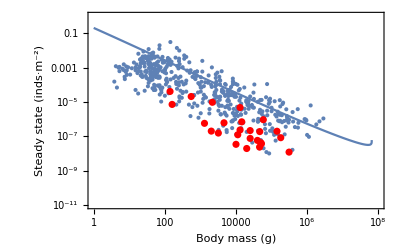

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5}],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*CsolNoPred/.{ξ->0,f->1},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
}]
```

Calculate Predator Yield

```mathematica
(*Yield of predator per prey*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
```

Calculate Consumer and Predator Boundary Densities

```mathematica
PreyDensityTheoreticalMax[M_] :=  Evaluate[YHerbperRes[M]*kRes//Simplify]; (*Grams Herb / m^2 given the mass of a predator and the optimal prey mass given predator mass conversion*)
PreyDensityTheoreticalHalfSat[M_]:=(PreyDensityTheoreticalMax[M]*(1-χ))/χ/.χ->0.99;
PredatorDensityTheoreticalMax[Mp_,M_]:= Evaluate[Ypred[Mp,M]*YHerbperRes[M]*kRes//Simplify];
```

Two Predator reproduction rates : linear to the theoretical maximum and M-M with saturation derived from the theoretical maximum

Plot::plln: Limiting value (3.87851×10^11 M^(3/4))/((1/(1-0.558075/M^(«20»)))^4. (0.291 (-1+(3.79423×10^7)/Power[«2»]^4.) M^0.92+(«11»+6.69691/M^(«20»)) M-(4.55308×10^8 M Log[(«21»)/Plus[«2»]])/(1/(1+Times[«1»]))^4.)) in {ConsumerDensity,0,(3.87851×10^11 M^(3/4))/((1/(1-0.558075/M^(«20»)))^4. (0.291 (-1+3.79423×10^7 Power[«2»]) M^0.92+(«11»+6.69691 Power[«2»]) M-(4.55308×10^8 M Log[0.0127415 Power[«2»]])/(1/Plus[«2»])^4.))} is not a machine-sized real number.

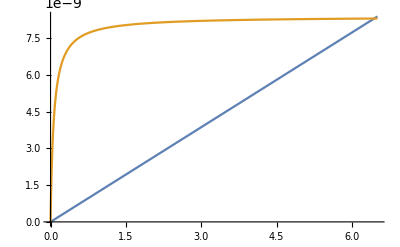

```mathematica
Plot[{λPred[OptPredMass[M]]*ConsumerDensity/PreyDensityTheoreticalMax[M],λPred[OptPredMass[M]]*(ConsumerDensity/(PreyDensityTheoreticalHalfSat[M]+ConsumerDensity))},{ConsumerDensity,0,PreyDensityTheoreticalMax[M]}]/.M->10^7
```

Plot the Theoretical Maxima for herbivore consumers and predators relative to Damuth Data

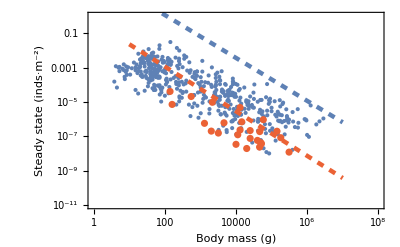

```mathematica
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M],{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/M)*PredatorDensityTheoreticalMax[OptPredMass[M],M],{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/figures/fig_maxdensities.pdf"}],PredPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2021_TaranWebs/figures/fig_maxdensities.pdf

Calculate per-capita Predation Mortality Rate as (predation rate per gram consumer)*(predated consumer density)

```mathematica
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[predgrowthrateperconsumer[Mp,M]*predatedconsumerdensity[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];

bP[M_] :=predmortalityfull[OptPredMass[M],M];
```

```mathematica
SSHarvest = (CsolNoPred/.{ξ->x,bP[M]->0,f->0});
SSNoHarvest = (CsolNoPred/.{ξ->0,bP[M]->0,f->0});
SSRHarvest = (RsolNoPred/.{ξ->x,bP[M]->0,f->0});
```

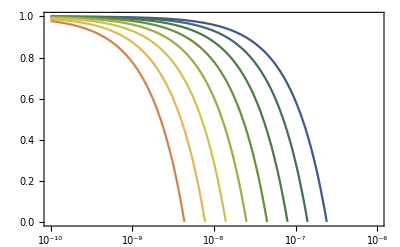

```mathematica
Show[
Table[LogLinearPlot[SSHarvest/SSNoHarvest/.{M->10^i},{x,10^-10,10^-6},PlotRange->{0,1},Frame->True,PlotStyle->ColorData["DarkRainbow",(i+1)/10]],{i,0,7}]
]
```

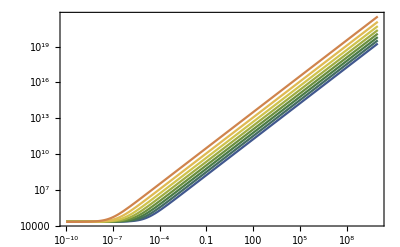

```mathematica
Show[
Table[LogLogPlot[SSRHarvest/.{M->10^i},{x,10^-10,10^10},PlotRange->All,Frame->True,PlotStyle->ColorData["DarkRainbow",(i+1)/10]],{i,0,7}]
]
```

```mathematica
ExtinctionHarvestRate=Table[{10^i,Select[Re[x/.NSolve[SSHarvest==0/.M->10^i,x]],#>0&][[1]]},{i,0,8,0.1}]
```

{{1.,2.39609×10^-7},{1.25893,2.2741×10^-7},{1.58489,2.15729×10^-7},{1.99526,2.04559×10^-7},{2.51189,1.93888×10^-7},{3.16228,1.83706×10^-7},{3.98107,1.73998×10^-7},{5.01187,1.64751×10^-7},{6.30957,1.5595×10^-7},{7.94328,1.47579×10^-7},{10.,1.39623×10^-7},{12.5893,1.32065×10^-7},{15.8489,1.24889×10^-7},{19.9526,1.1808×10^-7},{25.1189,1.11622×10^-7},{31.6228,1.05499×10^-7},{39.8107,9.96964×10^-8},{50.1187,9.41993×10^-8},{63.0957,8.89935×10^-8},{79.4328,8.40649×10^-8},{100.,7.94002×10^-8},{125.893,7.49864×10^-8},{158.489,7.0811×10^-8},{199.526,6.6862×10^-8},{251.189,6.3128×10^-8},{316.228,5.95979×10^-8},{398.107,5.62612×10^-8},{501.187,5.31078×10^-8},{630.957,5.01281×10^-8},{794.328,4.7313×10^-8},{1000.,4.46536×10^-8},{1258.93,4.21417×10^-8},{1584.89,3.97694×10^-8},{1995.26,3.75291×10^-8},{2511.89,3.54137×10^-8},{3162.28,3.34164×10^-8},{3981.07,3.15308×10^-8},{5011.87,2.97507×10^-8},{6309.57,2.80704×10^-8},{7943.28,2.64844×10^-8},{10000.,2.49875×10^-8},{12589.3,2.35747×10^-8},{15848.9,2.22414×10^-8},{19952.6,2.09831×10^-8},{25118.9,1.97958×10^-8},{31622.8,1.86754×10^-8},{39810.7,1.76182×10^-8},{50118.7,1.66206×10^-8},{63095.7,1.56795×10^-8},{79432.8,1.47915×10^-8},{100000.,1.39536×10^-8},{125893.,1.31632×10^-8},{158489.,1.24175×10^-8},{199526.,1.17139×10^-8},{251189.,1.10502×10^-8},{316228.,1.04241×10^-8},{398107.,9.83341×10^-9},{501187.,9.27618×10^-9},{630957.,8.75052×10^-9},{794328.,8.25464×10^-9},{1.×10^6,7.78686×10^-9},{1.25893×10^6,7.34559×10^-9},{1.58489×10^6,6.92933×10^-9},{1.99526×10^6,6.53667×10^-9},{2.51189×10^6,6.16626×10^-9},{3.16228×10^6,5.81685×10^-9},{3.98107×10^6,5.48726×10^-9},{5.01187×10^6,5.17635×10^-9},{6.30957×10^6,4.88306×10^-9},{7.94328×10^6,4.60641×10^-9},{1.×10^7,4.34544×10^-9},{1.25893×10^7,4.09927×10^-9},{1.58489×10^7,3.86706×10^-9},{1.99526×10^7,3.64802×10^-9},{2.51189×10^7,3.44139×10^-9},{3.16228×10^7,3.24648×10^-9},{3.98107×10^7,3.06262×10^-9},{5.01187×10^7,2.88919×10^-9},{6.30957×10^7,2.72558×10^-9},{7.94328×10^7,2.57125×10^-9},{1.×10^8,2.42567×10^-9}}

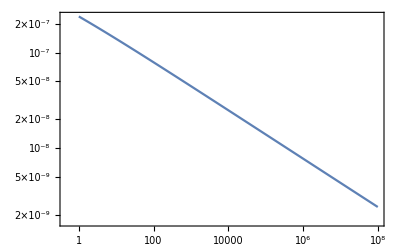

```mathematica
Show[{
ListLogLogPlot[ExtinctionHarvestRate,Frame->True,Joined->True](*,
LogLogPlot[λ[M],{M,1,10^7}]*)
}]
```

```mathematica
LinearModelFit[Log@ExtinctionHarvestRate,x,x]
```

FittedModel[-15.2036-0.250865 x]

```mathematica
ExtinctionPercentHarvestMortality =Table[{ExtinctionHarvestRate[[i,1]],( ExtinctionHarvestRate[[i,2]]/(σ[M]*(1-RsolNoPred/kRes)+μ[M]+ExtinctionHarvestRate[[i,2]]))/.{M->ExtinctionHarvestRate[[i,1]],ξ->ExtinctionHarvestRate[[i,2]]}},{i,1,Length[ExtinctionHarvestRate],1}]
```

{{1.,0.90361},{1.25893,0.909904},{1.58489,0.915786},{1.99526,0.921285},{2.51189,0.926425},{3.16228,0.93123},{3.98107,0.93572},{5.01187,0.939918},{6.30957,0.943841},{7.94328,0.947508},{10.,0.950936},{12.5893,0.95414},{15.8489,0.957134},{19.9526,0.959933},{25.1189,0.962549},{31.6228,0.964994},{39.8107,0.96728},{50.1187,0.969416},{63.0957,0.971412},{79.4328,0.973278},{100.,0.975022},{125.893,0.976652},{158.489,0.978176},{199.526,0.9796},{251.189,0.980931},{316.228,0.982175},{398.107,0.983338},{501.187,0.984424},{630.957,0.98544},{794.328,0.986389},{1000.,0.987277},{1258.93,0.988106},{1584.89,0.988882},{1995.26,0.989606},{2511.89,0.990283},{3162.28,0.990916},{3981.07,0.991508},{5011.87,0.992061},{6309.57,0.992578},{7943.28,0.993061},{10000.,0.993513},{12589.3,0.993935},{15848.9,0.99433},{19952.6,0.994699},{25118.9,0.995044},{31622.8,0.995366},{39810.7,0.995667},{50118.7,0.995949},{63095.7,0.996212},{79432.8,0.996458},{100000.,0.996688},{125893.,0.996904},{158489.,0.997105},{199526.,0.997293},{251189.,0.997468},{316228.,0.997633},{398107.,0.997786},{501187.,0.99793},{630957.,0.998064},{794328.,0.998189},{1.×10^6,0.998307},{1.25893×10^6,0.998416},{1.58489×10^6,0.998519},{1.99526×10^6,0.998615},{2.51189×10^6,0.998705},{3.16228×10^6,0.998788},{3.98107×10^6,0.998867},{5.01187×10^6,0.99894},{6.30957×10^6,0.999009},{7.94328×10^6,0.999073},{1.×10^7,0.999133},{1.25893×10^7,0.999189},{1.58489×10^7,0.999241},{1.99526×10^7,0.99929},{2.51189×10^7,0.999336},{3.16228×10^7,0.999379},{3.98107×10^7,0.999419},{5.01187×10^7,0.999456},{6.30957×10^7,0.999491},{7.94328×10^7,0.999524-3.49731×10^-15 ⅈ},{1.×10^8,0.999555-2.3802×10^-15 ⅈ}}

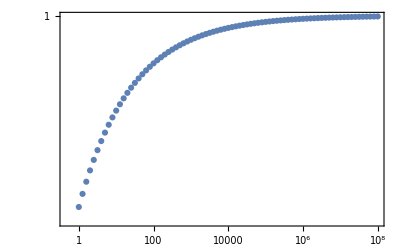

```mathematica
ListLogLogPlot[ExtinctionPercentHarvestMortality,Frame->True,PlotRange->All]
```

WITH PREDATION

```mathematica
SSHarvestWithPred = (Csol/.{ξ->x,f->1});
SSNoHarvestWithPred = (Csol/.{ξ->0,f->1});
SSHarvestWithGenPred = (Csol/.{ξ->x,f->0.37});
SSNoHarvestWithGenPred = (Csol/.{ξ->0,f->0.37});
```

```mathematica
ExtinctionHarvestRateWithPred=Table[{10^i,Select[Re[x/.NSolve[SSHarvestWithPred==0/.M->10^i,x]],#>0&][[1]]},{i,0,8,0.1}]
ExtinctionHarvestRateWithGenPred=Table[{10^i,Select[Re[x/.NSolve[SSHarvestWithGenPred==0/.M->10^i,x]],#>0&][[1]]},{i,0,8,0.1}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1.,2.39502×10^-7},{1.25893,2.27296×10^-7},{1.58489,2.15608×10^-7},{1.99526,2.04429×10^-7},{2.51189,1.9375×10^-7},{3.16228,1.83559×10^-7},{3.98107,1.73841×10^-7},{5.01187,1.64584×10^-7},{6.30957,1.55772×10^-7},{7.94328,1.4739×10^-7},{10.,1.39421×10^-7},{12.5893,1.3185×10^-7},{15.8489,1.2466×10^-7},{19.9526,1.17836×10^-7},{25.1189,1.11362×10^-7},{31.6228,1.05222×10^-7},{39.8107,9.94009×10^-8},{50.1187,9.38845×10^-8},{63.0957,8.8658×10^-8},{79.4328,8.37074×10^-8},{100.,7.90193×10^-8},{125.893,7.45805×10^-8},{158.489,7.03785×10^-8},{199.526,6.64013×10^-8},{251.189,6.26371×10^-8},{316.228,5.90749×10^-8},{398.107,5.57039×10^-8},{501.187,5.25141×10^-8},{630.957,4.94955×10^-8},{794.328,4.6639×10^-8},{1000.,4.39355×10^-8},{1258.93,4.13766×10^-8},{1584.89,3.89543×10^-8},{1995.26,3.66607×10^-8},{2511.89,3.44885×10^-8},{3162.28,3.24308×10^-8},{3981.07,3.04808×10^-8},{5011.87,2.86321×10^-8},{6309.57,2.68788×10^-8},{7943.28,2.5215×10^-8},{10000.,2.36352×10^-8},{12589.3,2.21343×10^-8},{15848.9,2.07071×10^-8},{19952.6,1.93489×10^-8},{25118.9,1.80551×10^-8},{31622.8,1.68214×10^-8},{39810.7,1.56436×10^-8},{50118.7,1.45178×10^-8},{63095.7,1.344×10^-8},{79432.8,1.24066×10^-8},{100000.,1.14142×10^-8},{125893.,1.04591×10^-8},{158489.,9.53834×10^-9},{199526.,8.64857×10^-9},{251189.,7.78677×10^-9},{316228.,6.94996×10^-9},{398107.,6.13527×10^-9},{501187.,5.33986×10^-9},{630957.,4.56101×10^-9},{794328.,3.79601×10^-9},{1.×10^6,3.04223×10^-9},{1.25893×10^6,2.29707×10^-9},{1.58489×10^6,1.55797×10^-9},{1.99526×10^6,8.22394×10^-10},{2.51189×10^6,8.78369×10^-11},{3.16228×10^6,{}⟦1⟧},{3.98107×10^6,{}⟦1⟧},{5.01187×10^6,{}⟦1⟧},{6.30957×10^6,{}⟦1⟧},{7.94328×10^6,{}⟦1⟧},{1.×10^7,{}⟦1⟧},{1.25893×10^7,{}⟦1⟧},{1.58489×10^7,{}⟦1⟧},{1.99526×10^7,{}⟦1⟧},{2.51189×10^7,{}⟦1⟧},{3.16228×10^7,{}⟦1⟧},{3.98107×10^7,{}⟦1⟧},{5.01187×10^7,{}⟦1⟧},{6.30957×10^7,{}⟦1⟧},{7.94328×10^7,{}⟦1⟧},{1.×10^8,{}⟦1⟧}}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1.,2.3957×10^-7},{1.25893,2.27368×10^-7},{1.58489,2.15684×10^-7},{1.99526,2.04511×10^-7},{2.51189,1.93837×10^-7},{3.16228,1.83651×10^-7},{3.98107,1.7394×10^-7},{5.01187,1.64689×10^-7},{6.30957,1.55884×10^-7},{7.94328,1.47509×10^-7},{10.,1.39548×10^-7},{12.5893,1.31985×10^-7},{15.8489,1.24804×10^-7},{19.9526,1.1799×10^-7},{25.1189,1.11525×10^-7},{31.6228,1.05396×10^-7},{39.8107,9.95871×10^-8},{50.1187,9.40828×10^-8},{63.0957,8.88693×10^-8},{79.4328,8.39326×10^-8},{100.,7.92592×10^-8},{125.893,7.48362×10^-8},{158.489,7.0651×10^-8},{199.526,6.66915×10^-8},{251.189,6.29464×10^-8},{316.228,5.94044×10^-8},{398.107,5.6055×10^-8},{501.187,5.28881×10^-8},{630.957,4.98941×10^-8},{794.328,4.70636×10^-8},{1000.,4.43879×10^-8},{1258.93,4.18586×10^-8},{1584.89,3.94678×10^-8},{1995.26,3.72078×10^-8},{2511.89,3.50714×10^-8},{3162.28,3.30517×10^-8},{3981.07,3.11423×10^-8},{5011.87,2.93368×10^-8},{6309.57,2.76295×10^-8},{7943.28,2.60147×10^-8},{10000.,2.44871×10^-8},{12589.3,2.30417×10^-8},{15848.9,2.16737×10^-8},{19952.6,2.03784×10^-8},{25118.9,1.91517×10^-8},{31622.8,1.79894×10^-8},{39810.7,1.68876×10^-8},{50118.7,1.58426×10^-8},{63095.7,1.48509×10^-8},{79432.8,1.39091×10^-8},{100000.,1.3014×10^-8},{125893.,1.21627×10^-8},{158489.,1.13522×10^-8},{199526.,1.05798×10^-8},{251189.,9.84275×10^-9},{316228.,9.13867×10^-9},{398107.,8.4651×10^-9},{501187.,7.81975×10^-9},{630957.,7.2004×10^-9},{794328.,6.60495×10^-9},{1.×10^6,6.03135×10^-9},{1.25893×10^6,5.47764×10^-9},{1.58489×10^6,4.94193×10^-9},{1.99526×10^6,4.42238×10^-9},{2.51189×10^6,3.91724×10^-9},{3.16228×10^6,3.42478×10^-9},{3.98107×10^6,2.94333×10^-9},{5.01187×10^6,2.47127×10^-9},{6.30957×10^6,2.007×10^-9},{7.94328×10^6,1.54898×10^-9},{1.×10^7,1.09568×10^-9},{1.25893×10^7,6.45599×10^-10},{1.58489×10^7,1.97273×10^-10},{1.99526×10^7,{}⟦1⟧},{2.51189×10^7,{}⟦1⟧},{3.16228×10^7,{}⟦1⟧},{3.98107×10^7,{}⟦1⟧},{5.01187×10^7,{}⟦1⟧},{6.30957×10^7,{}⟦1⟧},{7.94328×10^7,{}⟦1⟧},{1.×10^8,{}⟦1⟧}}

```mathematica
ExtinctionPercentHarvestMortalityWithPred =Table[{ExtinctionHarvestRateWithPred[[i,1]],( ExtinctionHarvestRateWithPred[[i,2]]/(σ[M]*(1-(Rsol/.f->1)/kRes)+μ[M]+bP[M]+ExtinctionHarvestRateWithPred[[i,2]]))/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}]
```

{{1.,0.903206},{1.25893,0.909447},{1.58489,0.91527},{1.99526,0.920702},{2.51189,0.925766},{3.16228,0.930484},{3.98107,0.934878},{5.01187,0.938966},{6.30957,0.942765},{7.94328,0.946292},{10.,0.949561},{12.5893,0.952585},{15.8489,0.955377},{19.9526,0.957947},{25.1189,0.960304},{31.6228,0.962457},{39.8107,0.964412},{50.1187,0.966175},{63.0957,0.96775},{79.4328,0.969139},{100.,0.970345},{125.893,0.971366},{158.489,0.972202},{199.526,0.972849},{251.189,0.973302},{316.228,0.973555},{398.107,0.973597},{501.187,0.973418},{630.957,0.973003},{794.328,0.972337},{1000.,0.971399},{1258.93,0.970167},{1584.89,0.968613},{1995.26,0.966707},{2511.89,0.964412},{3162.28,0.961688},{3981.07,0.958489},{5011.87,0.95476},{6309.57,0.950441},{7943.28,0.945463},{10000.,0.939748},{12589.3,0.933206},{15848.9,0.925737},{19952.6,0.917227},{25118.9,0.907548},{31622.8,0.896553},{39810.7,0.884079},{50118.7,0.86994},{63095.7,0.853925},{79432.8,0.8358},{100000.,0.815296},{125893.,0.792114},{158489.,0.765914},{199526.,0.736315},{251189.,0.702886},{316228.,0.665143},{398107.,0.622539},{501187.,0.574461},{630957.,0.520218},{794328.,0.459031},{1.×10^6,0.390026},{1.25893×10^6,0.312218},{1.58489×10^6,0.224503},{1.99526×10^6,0.125638},{2.51189×10^6,0.0142263},{3.16228×10^6,{}⟦1⟧/(6.47211×10^-9+{}⟦1⟧+1.21598×10^-7 (1-89.389 (23000 (1.21598×10^-7+2 (-2.26375×10^-9+{}⟦1⟧))+23000 √((1.21598×10^-7+2 (-2.26375×10^-9+{}⟦1⟧))^2+9.72788×10^-7 (1.28071×10^-7+{}⟦1⟧)))))},{3.98107×10^6,{}⟦1⟧/(6.88169×10^-9+{}⟦1⟧+1.09831×10^-7 (1-98.9664 (23000 (1.09831×10^-7+2 (-1.35853×10^-9+{}⟦1⟧))+23000 √((1.09831×10^-7+2 (-1.35853×10^-9+{}⟦1⟧))^2+8.78647×10^-7 (1.16713×10^-7+{}⟦1⟧)))))},{5.01187×10^6,{}⟦1⟧/(7.31651×10^-9+{}⟦1⟧+9.89283×10^-8 (1-109.873 (23000 (9.89283×10^-8+2 (-4.56251×10^-10+{}⟦1⟧))+23000 √((9.89283×10^-8+2 (-4.56251×10^-10+{}⟦1⟧))^2+7.91426×10^-7 (1.06245×10^-7+{}⟦1⟧)))))},{6.30957×10^6,{}⟦1⟧/(7.77798×10^-9+{}⟦1⟧+8.88276×10^-8 (1-122.367 (23000 (8.88276×10^-8+2 (4.46116×10^-10+{}⟦1⟧))+23000 √(7.10621×10^-7 (9.66056×10^-8+{}⟦1⟧)+(8.88276×10^-8+2 (4.46116×10^-10+{}⟦1⟧))^2))))},{7.94328×10^6,{}⟦1⟧/(8.2676×10^-9+{}⟦1⟧+7.94677×10^-8 (1-136.78 (23000 (7.94677×10^-8+2 (1.35157×10^-9+{}⟦1⟧))+23000 √(6.35742×10^-7 (8.77353×10^-8+{}⟦1⟧)+(7.94677×10^-8+2 (1.35157×10^-9+{}⟦1⟧))^2))))},{1.×10^7,{}⟦1⟧/(8.78692×10^-9+{}⟦1⟧+7.07889×10^-8 (1-153.549 (23000 (7.07889×10^-8+2 (2.2631×10^-9+{}⟦1⟧))+23000 √(5.66311×10^-7 (7.95758×10^-8+{}⟦1⟧)+(7.07889×10^-8+2 (2.2631×10^-9+{}⟦1⟧))^2))))},{1.25893×10^7,{}⟦1⟧/(9.33758×10^-9+{}⟦1⟧+6.27314×10^-8 (1-173.271 (23000 (6.27314×10^-8+2 (3.18368×10^-9+{}⟦1⟧))+23000 √(5.01851×10^-7 (7.2069×10^-8+{}⟦1⟧)+(6.27314×10^-8+2 (3.18368×10^-9+{}⟦1⟧))^2))))},{1.58489×10^7,{}⟦1⟧/(9.92129×10^-9+{}⟦1⟧+5.5234×10^-8 (1-196.791 (23000 (5.5234×10^-8+2 (4.11629×10^-9+{}⟦1⟧))+23000 √(4.41872×10^-7 (6.51553×10^-8+{}⟦1⟧)+(5.5234×10^-8+2 (4.11629×10^-9+{}⟦1⟧))^2))))},{1.99526×10^7,{}⟦1⟧/(1.05398×10^-8+{}⟦1⟧+4.82304×10^-8 (1-225.367 (23000 (4.82304×10^-8+2 (5.0639×10^-9+{}⟦1⟧))+23000 √(3.85843×10^-7 (5.87702×10^-8+{}⟦1⟧)+(4.82304×10^-8+2 (5.0639×10^-9+{}⟦1⟧))^2))))},{2.51189×10^7,{}⟦1⟧/(1.1195×10^-8+{}⟦1⟧+4.1643×10^-8 (1-261.018 (23000 (4.1643×10^-8+2 (6.02951×10^-9+{}⟦1⟧))+23000 √(3.33144×10^-7 (5.2838×10^-8+{}⟦1⟧)+(4.1643×10^-8+2 (6.02951×10^-9+{}⟦1⟧))^2))))},{3.16228×10^7,{}⟦1⟧/(1.18889×10^-8+{}⟦1⟧+3.53679×10^-8 (1-307.329 (23000 (3.53679×10^-8+2 (7.01611×10^-9+{}⟦1⟧))+23000 √(2.82943×10^-7 (4.72567×10^-8+{}⟦1⟧)+(3.53679×10^-8+2 (7.01611×10^-9+{}⟦1⟧))^2))))},{3.98107×10^7,{}⟦1⟧/(1.26233×10^-8+{}⟦1⟧+2.92341×10^-8 (1-371.811 (23000 (2.92341×10^-8+2 (8.02671×10^-9+{}⟦1⟧))+23000 √(2.33873×10^-7 (4.18574×10^-8+{}⟦1⟧)+(2.92341×10^-8+2 (8.02671×10^-9+{}⟦1⟧))^2))))},{5.01187×10^7,{}⟦1⟧/(1.34005×10^-8+{}⟦1⟧+2.28408×10^-8 (1-475.884 (23000 (2.28408×10^-8+2 (9.06437×10^-9+{}⟦1⟧))+23000 √(1.82726×10^-7 (3.62413×10^-8+{}⟦1⟧)+(2.28408×10^-8+2 (9.06437×10^-9+{}⟦1⟧))^2))))},{6.30957×10^7,{}⟦1⟧/(1.42226×10^-8+{}⟦1⟧+1.37381×10^-8 (1-791.198 (23000 (1.37381×10^-8+2 (1.01321×10^-8+{}⟦1⟧))+23000 √(1.09905×10^-7 (2.79607×10^-8+{}⟦1⟧)+(1.37381×10^-8+2 (1.01321×10^-8+{}⟦1⟧))^2))))},{7.94328×10^7,{}⟦1⟧/(1.50918×10^-8+{}⟦1⟧+(1.11383×10^-8+9.30307×10^-9 ⅈ) (1-(574.85-480.134 ⅈ) (23000 ((1.11383×10^-8+9.30307×10^-9 ⅈ)+2 (1.12331×10^-8+{}⟦1⟧))+23000 √((8.91063×10^-8+7.44245×10^-8 ⅈ) ((2.62301×10^-8+9.30307×10^-9 ⅈ)+{}⟦1⟧)+((1.11383×10^-8+9.30307×10^-9 ⅈ)+2 (1.12331×10^-8+{}⟦1⟧))^2))))},{1.×10^8,{}⟦1⟧/(1.60105×10^-8+{}⟦1⟧+(1.06669×10^-8+1.13262×10^-8 ⅈ) (1-(478.98-508.583 ⅈ) (23000 ((1.06669×10^-8+1.13262×10^-8 ⅈ)+2 (1.23704×10^-8+{}⟦1⟧))+23000 √((8.53354×10^-8+9.06096×10^-8 ⅈ) ((2.66774×10^-8+1.13262×10^-8 ⅈ)+{}⟦1⟧)+((1.06669×10^-8+1.13262×10^-8 ⅈ)+2 (1.23704×10^-8+{}⟦1⟧))^2))))}}

```mathematica
ExtinctionPercentHarvestMortalityWithGenPred =Table[{ExtinctionHarvestRateWithGenPred[[i,1]],( ExtinctionHarvestRateWithGenPred[[i,2]]/(σ[M]*(1-(Rsol/.f->0.37)/kRes)+μ[M]+0.37*bP[M]+ExtinctionHarvestRateWithGenPred[[i,2]]))/.{M->ExtinctionHarvestRateWithGenPred[[i,1]],ξ->ExtinctionHarvestRateWithGenPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithGenPred],1}]
```

{{1.,0.903461},{1.25893,0.909735},{1.58489,0.915595},{1.99526,0.92107},{2.51189,0.926181},{3.16228,0.930954},{3.98107,0.935409},{5.01187,0.939566},{6.30957,0.943443},{7.94328,0.947058},{10.,0.950427},{12.5893,0.953565},{15.8489,0.956484},{19.9526,0.959198},{25.1189,0.961719},{31.6228,0.964056},{39.8107,0.966219},{50.1187,0.968217},{63.0957,0.970057},{79.4328,0.971747},{100.,0.973291},{125.893,0.974696},{158.489,0.975965},{199.526,0.977102},{251.189,0.978108},{316.228,0.978985},{398.107,0.979734},{501.187,0.980352},{630.957,0.980838},{794.328,0.98119},{1000.,0.981402},{1258.93,0.981469},{1584.89,0.981382},{1995.26,0.981133},{2511.89,0.980711},{3162.28,0.980102},{3981.07,0.979291},{5011.87,0.97826},{6309.57,0.976988},{7943.28,0.97545},{10000.,0.97362},{12589.3,0.971465},{15848.9,0.968951},{19952.6,0.966034},{25118.9,0.96267},{31622.8,0.958805},{39810.7,0.95438},{50118.7,0.949326},{63095.7,0.943566},{79432.8,0.937015},{100000.,0.929573},{125893.,0.921131},{158489.,0.911564},{199526.,0.900731},{251189.,0.888473},{316228.,0.874611},{398107.,0.858945},{501187.,0.841246},{630957.,0.821261},{794328.,0.798701},{1.×10^6,0.773243},{1.25893×10^6,0.744523},{1.58489×10^6,0.712133},{1.99526×10^6,0.675613},{2.51189×10^6,0.634448},{3.16228×10^6,0.588056},{3.98107×10^6,0.535787},{5.01187×10^6,0.47691},{6.30957×10^6,0.410606},{7.94328×10^6,0.335954},{1.×10^7,0.251925},{1.25893×10^7,0.157363},{1.58489×10^7,0.0509749},{1.99526×10^7,{}⟦1⟧/(3.90136×10^-9+{}⟦1⟧+4.82304×10^-8 (1-225.367 (23000 (4.82304×10^-8+2 (-1.57455×10^-9+{}⟦1⟧))+23000 √((4.82304×10^-8+2 (-1.57455×10^-9+{}⟦1⟧))^2+3.85843×10^-7 (5.21318×10^-8+{}⟦1⟧)))))},{2.51189×10^7,{}⟦1⟧/(4.1436×10^-9+{}⟦1⟧+4.1643×10^-8 (1-261.018 (23000 (4.1643×10^-8+2 (-1.02192×10^-9+{}⟦1⟧))+23000 √((4.1643×10^-8+2 (-1.02192×10^-9+{}⟦1⟧))^2+3.33144×10^-7 (4.57866×10^-8+{}⟦1⟧)))))},{3.16228×10^7,{}⟦1⟧/(4.40015×10^-9+{}⟦1⟧+3.53679×10^-8 (1-307.329 (23000 (3.53679×10^-8+2 (-4.72601×10^-10+{}⟦1⟧))+23000 √((3.53679×10^-8+2 (-4.72601×10^-10+{}⟦1⟧))^2+2.82943×10^-7 (3.9768×10^-8+{}⟦1⟧)))))},{3.98107×10^7,{}⟦1⟧/(4.67175×10^-9+{}⟦1⟧+2.92341×10^-8 (1-371.811 (23000 (2.92341×10^-8+2 (7.51456×10^-11+{}⟦1⟧))+23000 √(2.33873×10^-7 (3.39059×10^-8+{}⟦1⟧)+(2.92341×10^-8+2 (7.51456×10^-11+{}⟦1⟧))^2))))},{5.01187×10^7,{}⟦1⟧/(4.95918×10^-9+{}⟦1⟧+2.28408×10^-8 (1-475.884 (23000 (2.28408×10^-8+2 (6.23041×10^-10+{}⟦1⟧))+23000 √(1.82726×10^-7 (2.78×10^-8+{}⟦1⟧)+(2.28408×10^-8+2 (6.23041×10^-10+{}⟦1⟧))^2))))},{6.30957×10^7,{}⟦1⟧/(5.26323×10^-9+{}⟦1⟧+1.37381×10^-8 (1-791.198 (23000 (1.37381×10^-8+2 (1.17278×10^-9+{}⟦1⟧))+23000 √(1.09905×10^-7 (1.90013×10^-8+{}⟦1⟧)+(1.37381×10^-8+2 (1.17278×10^-9+{}⟦1⟧))^2))))},{7.94328×10^7,{}⟦1⟧/(5.58474×10^-9+{}⟦1⟧+(1.11383×10^-8+9.30307×10^-9 ⅈ) (1-(574.85-480.134 ⅈ) (23000 ((1.11383×10^-8+9.30307×10^-9 ⅈ)+2 (1.72602×10^-9+{}⟦1⟧))+23000 √((8.91063×10^-8+7.44245×10^-8 ⅈ) ((1.6723×10^-8+9.30307×10^-9 ⅈ)+{}⟦1⟧)+((1.11383×10^-8+9.30307×10^-9 ⅈ)+2 (1.72602×10^-9+{}⟦1⟧))^2))))},{1.×10^8,{}⟦1⟧/(5.92457×10^-9+{}⟦1⟧+(1.06669×10^-8+1.13262×10^-8 ⅈ) (1-(478.98-508.583 ⅈ) (23000 ((1.06669×10^-8+1.13262×10^-8 ⅈ)+2 (2.28443×10^-9+{}⟦1⟧))+23000 √((8.53354×10^-8+9.06096×10^-8 ⅈ) ((1.65915×10^-8+1.13262×10^-8 ⅈ)+{}⟦1⟧)+((1.06669×10^-8+1.13262×10^-8 ⅈ)+2 (2.28443×10^-9+{}⟦1⟧))^2))))}}

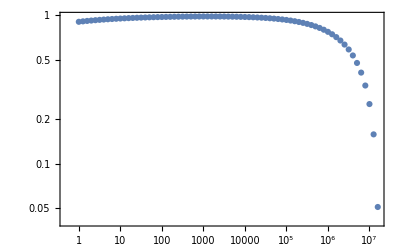

```mathematica
ListLogLogPlot[ExtinctionPercentHarvestMortalityWithGenPred,Frame->True]
```

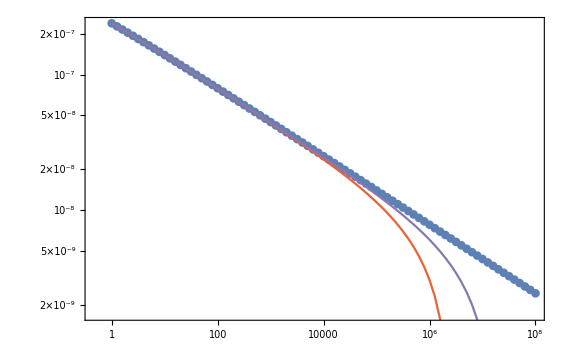

```mathematica
Show[{
ListLogLogPlot[ExtinctionHarvestRate,Frame->True],
ListLogLogPlot[ExtinctionHarvestRateWithPred,PlotStyle->ColorData[97,4],Frame->True,Joined->True],
ListLogLogPlot[ExtinctionHarvestRateWithGenPred,PlotStyle->ColorData[97,5],Frame->True,Joined->True]
}]
```

```mathematica
lm=LinearModelFit[Log@ExtinctionHarvestRate,x,x]
```

FittedModel[-15.2036-0.250865 x]

```mathematica
Table[ColorData[97,i],{i,1,20,1}]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.838355547812947, 0.44746667828057946, 0.0208888695323676],RGBColor[0.5833680111493557, 0.4126186601628758, 0.8290799721266107],RGBColor[0.8996399512215667, 0.7463488834690629, 0.],RGBColor[0.8439466852489265, 0.3467106629502147, 0.3309221912517893],RGBColor[0.28240003484173815, 0.6090799721266095, 0.7538800418100857]}

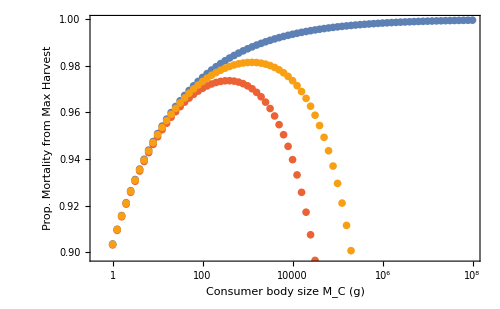

```mathematica
Show[{
ListLogLinearPlot[ExtinctionPercentHarvestMortality,Frame->True,FrameLabel->{"Consumer body size M_C (g)","Prop. Mortality from Max Harvest"},LabelStyle->Directive[FontSize->16]],
ListLogLinearPlot[ExtinctionPercentHarvestMortalityWithPred,Frame->True,PlotStyle->ColorData[97,4]],
ListLogLinearPlot[ExtinctionPercentHarvestMortalityWithGenPred,Frame->True,PlotStyle->ColorData[97,13]]
},ImageSize->500]
```

```mathematica
Max[Re[ExtinctionPercentHarvestMortalityWithPred[[All,2]]]]
```

Max[0.973597,Re[{}⟦1⟧/(7.31651×10^-9+{}⟦1⟧+9.89283×10^-8 (1-109.873 (23000 (9.89283×10^-8+2 (-4.56251×10^-10+{}⟦1⟧))+23000 √((9.89283×10^-8+2 (-4.56251×10^-10+{}⟦1⟧))^2+7.91426×10^-7 (1.06245×10^-7+{}⟦1⟧)))))],Re[{}⟦1⟧/(6.88169×10^-9+{}⟦1⟧+1.09831×10^-7 (1-98.9664 (23000 (1.09831×10^-7+2 (-1.35853×10^-9+{}⟦1⟧))+23000 √((1.09831×10^-7+2 (-1.35853×10^-9+{}⟦1⟧))^2+8.78647×10^-7 (1.16713×10^-7+{}⟦1⟧)))))],Re[{}⟦1⟧/(6.47211×10^-9+{}⟦1⟧+1.21598×10^-7 (1-89.389 (23000 (1.21598×10^-7+2 (-2.26375×10^-9+{}⟦1⟧))+23000 √((1.21598×10^-7+2 (-2.26375×10^-9+{}⟦1⟧))^2+9.72788×10^-7 (1.28071×10^-7+{}⟦1⟧)))))],Re[{}⟦1⟧/(7.77798×10^-9+{}⟦1⟧+8.88276×10^-8 (1-122.367 (23000 (8.88276×10^-8+2 (4.46116×10^-10+{}⟦1⟧))+23000 √(7.10621×10^-7 (9.66056×10^-8+{}⟦1⟧)+(8.88276×10^-8+2 (4.46116×10^-10+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(8.2676×10^-9+{}⟦1⟧+7.94677×10^-8 (1-136.78 (23000 (7.94677×10^-8+2 (1.35157×10^-9+{}⟦1⟧))+23000 √(6.35742×10^-7 (8.77353×10^-8+{}⟦1⟧)+(7.94677×10^-8+2 (1.35157×10^-9+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(8.78692×10^-9+{}⟦1⟧+7.07889×10^-8 (1-153.549 (23000 (7.07889×10^-8+2 (2.2631×10^-9+{}⟦1⟧))+23000 √(5.66311×10^-7 (7.95758×10^-8+{}⟦1⟧)+(7.07889×10^-8+2 (2.2631×10^-9+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(9.33758×10^-9+{}⟦1⟧+6.27314×10^-8 (1-173.271 (23000 (6.27314×10^-8+2 (3.18368×10^-9+{}⟦1⟧))+23000 √(5.01851×10^-7 (7.2069×10^-8+{}⟦1⟧)+(6.27314×10^-8+2 (3.18368×10^-9+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(9.92129×10^-9+{}⟦1⟧+5.5234×10^-8 (1-196.791 (23000 (5.5234×10^-8+2 (4.11629×10^-9+{}⟦1⟧))+23000 √(4.41872×10^-7 (6.51553×10^-8+{}⟦1⟧)+(5.5234×10^-8+2 (4.11629×10^-9+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(1.05398×10^-8+{}⟦1⟧+4.82304×10^-8 (1-225.367 (23000 (4.82304×10^-8+2 (5.0639×10^-9+{}⟦1⟧))+23000 √(3.85843×10^-7 (5.87702×10^-8+{}⟦1⟧)+(4.82304×10^-8+2 (5.0639×10^-9+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(1.1195×10^-8+{}⟦1⟧+4.1643×10^-8 (1-261.018 (23000 (4.1643×10^-8+2 (6.02951×10^-9+{}⟦1⟧))+23000 √(3.33144×10^-7 (5.2838×10^-8+{}⟦1⟧)+(4.1643×10^-8+2 (6.02951×10^-9+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(1.18889×10^-8+{}⟦1⟧+3.53679×10^-8 (1-307.329 (23000 (3.53679×10^-8+2 (7.01611×10^-9+{}⟦1⟧))+23000 √(2.82943×10^-7 (4.72567×10^-8+{}⟦1⟧)+(3.53679×10^-8+2 (7.01611×10^-9+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(1.26233×10^-8+{}⟦1⟧+2.92341×10^-8 (1-371.811 (23000 (2.92341×10^-8+2 (8.02671×10^-9+{}⟦1⟧))+23000 √(2.33873×10^-7 (4.18574×10^-8+{}⟦1⟧)+(2.92341×10^-8+2 (8.02671×10^-9+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(1.34005×10^-8+{}⟦1⟧+2.28408×10^-8 (1-475.884 (23000 (2.28408×10^-8+2 (9.06437×10^-9+{}⟦1⟧))+23000 √(1.82726×10^-7 (3.62413×10^-8+{}⟦1⟧)+(2.28408×10^-8+2 (9.06437×10^-9+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(1.42226×10^-8+{}⟦1⟧+1.37381×10^-8 (1-791.198 (23000 (1.37381×10^-8+2 (1.01321×10^-8+{}⟦1⟧))+23000 √(1.09905×10^-7 (2.79607×10^-8+{}⟦1⟧)+(1.37381×10^-8+2 (1.01321×10^-8+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(1.50918×10^-8+{}⟦1⟧+(1.11383×10^-8+9.30307×10^-9 ⅈ) (1-(574.85-480.134 ⅈ) (23000 ((1.11383×10^-8+9.30307×10^-9 ⅈ)+2 (1.12331×10^-8+{}⟦1⟧))+23000 √((8.91063×10^-8+7.44245×10^-8 ⅈ) ((2.62301×10^-8+9.30307×10^-9 ⅈ)+{}⟦1⟧)+((1.11383×10^-8+9.30307×10^-9 ⅈ)+2 (1.12331×10^-8+{}⟦1⟧))^2))))],Re[{}⟦1⟧/(1.60105×10^-8+{}⟦1⟧+(1.06669×10^-8+1.13262×10^-8 ⅈ) (1-(478.98-508.583 ⅈ) (23000 ((1.06669×10^-8+1.13262×10^-8 ⅈ)+2 (1.23704×10^-8+{}⟦1⟧))+23000 √((8.53354×10^-8+9.06096×10^-8 ⅈ) ((2.66774×10^-8+1.13262×10^-8 ⅈ)+{}⟦1⟧)+((1.06669×10^-8+1.13262×10^-8 ⅈ)+2 (1.23704×10^-8+{}⟦1⟧))^2))))]]

```mathematica
(*MaxPercentExtinctionPosition = Position[Re[ExtinctionPercentHarvestMortalityWithPred[[All,2]]],Max[Re[ExtinctionPercentHarvestMortalityWithPred[[All,2]]]]][[1]][[1]];
ExtinctionPercentHarvestMortalityWithPred[[MaxPercentExtinctionPosition,All]]*)
```

```mathematica
(*ExtinctionHarvestRateVsReproductionRate = Table[{ExtinctionHarvestRateWithPred[[i,1]],( ExtinctionHarvestRateWithPred[[i,2]]/(λ[M]))/.{M->ExtinctionHarvestRateWithPred[[i,1]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}];*)
```

```mathematica
(*ListLogLinearPlot[ExtinctionHarvestRateVsReproductionRate,Frame->True,FrameLabel->{"Consumer body size M_C (g)","ξ/λ"}]*)
```

```mathematica
(*PercentAddedMortalityHarvesting = Table[{ExtinctionHarvestRateWithPred[[i,1]],( ((σ[M]*(1-Rsol/kRes)+μ[M]+bP[M]+ExtinctionHarvestRateWithPred[[i,2]])-(σ[M]*(1-Rsol/kRes)+μ[M]+bP[M]))/(σ[M]*(1-Rsol/kRes)+μ[M]+bP[M]))/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}];*)
```

```mathematica
(*ScaledExtinctionHarvestRate =Table[{ExtinctionHarvestRateWithPred[[i,1]],ξ*(1/ExtinctionHarvestRateWithPred[[i,1]])*SSNoHarvestWithPred/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}]*)
```

```mathematica
(*ListLogLogPlot[ScaledExtinctionHarvestRate]*)
```

How many generations to extinction?

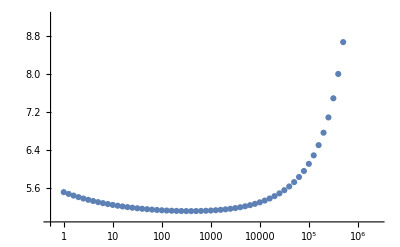

```mathematica
ListLogLinearPlot[Table[{ExtinctionHarvestRateWithPred[[i,1]],Log[0.1]/(-ξ*τLam[M])/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}]
]
```

How many years to extinction?

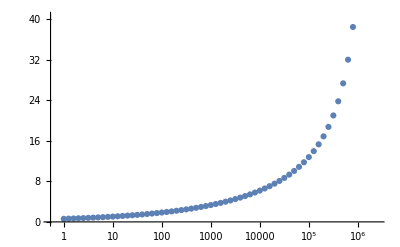

```mathematica
ListLogLinearPlot[Table[{ExtinctionHarvestRateWithPred[[i,1]],(Log[0.01]/(-ξ))*((1/60)*(1/60)*(1/24)*(1/365))/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}]
]
```

```mathematica
fractionremain = 0.01;
areaharvested =4.24*10^11;(* 2.45*10^13;*) (*meters^2*)
IndsHarvestedPerYear=Table[{ExtinctionHarvestRate[[i,1]],(SSNoHarvest*(1-fractionremain))/(M*(Log[fractionremain]/(-ξ)))*(60*60*24*365)*(areaharvested)}/.{M->ExtinctionHarvestRate[[i,1]],ξ->ExtinctionHarvestRate[[i,2]]},{i,1,Length[ExtinctionHarvestRate],1}];
IndsHarvestedPerYearPred=Table[{ExtinctionHarvestRateWithPred[[i,1]],(SSNoHarvestWithPred*(1-fractionremain))/(M*(Log[fractionremain]/(-ξ)))*(60*60*24*365)*(areaharvested)}/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]},{i,1,Length[ExtinctionHarvestRateWithPred],1}];
IndsHarvestedPerYearGenPred=Table[{ExtinctionHarvestRateWithGenPred[[i,1]],(SSNoHarvestWithGenPred*(1-fractionremain))/(M*(Log[fractionremain]/(-ξ)))*(60*60*24*365)*(areaharvested)}/.{M->ExtinctionHarvestRateWithGenPred[[i,1]],ξ->ExtinctionHarvestRateWithGenPred[[i,2]]},{i,1,Length[ExtinctionHarvestRateWithGenPred],1}];
IndsHarvestedPerYearTime=Table[{ExtinctionHarvestRate[[i,1]],(Log[fractionremain]/(-ξ))*((1/60)*(1/60)*(1/24)*(1/365))/.{M->ExtinctionHarvestRate[[i,1]],ξ->ExtinctionHarvestRate[[i,2]]}},{i,1,Length[ExtinctionHarvestRate],1}];
IndsHarvestedPerYearTimeWithPred=Table[{ExtinctionHarvestRateWithPred[[i,1]],(Log[0.01]/(-ξ))*((1/60)*(1/60)*(1/24)*(1/365))/.{M->ExtinctionHarvestRateWithPred[[i,1]],ξ->ExtinctionHarvestRateWithPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithPred],1}];
IndsHarvestedPerYearTimeWithGenPred=Table[{ExtinctionHarvestRateWithGenPred[[i,1]],(Log[0.01]/(-ξ))*((1/60)*(1/60)*(1/24)*(1/365))/.{M->ExtinctionHarvestRateWithGenPred[[i,1]],ξ->ExtinctionHarvestRateWithGenPred[[i,2]]}},{i,1,Length[ExtinctionHarvestRateWithGenPred],1}];
```

```mathematica
IndsHarvestedPerYear
```

{{1.,1.41395×10^11},{1.25893,1.08419×10^11},{1.58489,8.3035×10^10},{1.99526,6.35243×10^10},{2.51189,4.85492×10^10},{3.16228,3.707×10^10},{3.98107,2.8281×10^10},{5.01187,2.15591×10^10},{6.30957,1.64232×10^10},{7.94328,1.25027×10^10},{10.,9.51255×10^9},{12.5893,7.23367×10^9},{15.8489,5.49811×10^9},{19.9526,4.17717×10^9},{25.1189,3.17239×10^9},{31.6228,2.40849×10^9},{39.8107,1.828×10^9},{50.1187,1.38707×10^9},{63.0957,1.05228×10^9},{79.4328,7.9815×10^8},{100.,6.05312×10^8},{125.893,4.59017×10^8},{158.489,3.48055×10^8},{199.526,2.63907×10^8},{251.189,2.00102×10^8},{316.228,1.51727×10^8},{398.107,1.15053×10^8},{501.187,8.72502×10^7},{630.957,6.61736×10^7},{794.328,5.01953×10^7},{1000.,3.80814×10^7},{1258.93,2.88967×10^7},{1584.89,2.1932×10^7},{1995.26,1.665×10^7},{2511.89,1.26436×10^7},{3162.28,9.60404×10^6},{3981.07,7.29759×10^6},{5011.87,5.54699×10^6},{6309.57,4.21793×10^6},{7943.28,3.20861×10^6},{10000.,2.44186×10^6},{12589.3,1.85919×10^6},{15848.9,1.41624×10^6},{19952.6,1.07938×10^6},{25118.9,823092.},{31622.8,628016.},{39810.7,479463.},{50118.7,366283.},{63095.7,280007.},{79432.8,214204.},{100000.,163987.},{125893.,125640.},{158489.,96340.},{199526.,73936.9},{251189.,56795.5},{316228.,43670.4},{398107.,33612.9},{501187.,25899.8},{630957.,19979.7},{794328.,15431.9},{1.×10^6,11935.},{1.25893×10^6,9243.67},{1.58489×10^6,7170.22},{1.99526×10^6,5571.15},{2.51189×10^6,4336.6},{3.16228×10^6,3382.41},{3.98107×10^6,2644.06},{5.01187×10^6,2072.08},{6.30957×10^6,1628.46},{7.94328×10^6,1284.02},{1.×10^7,1016.35},{1.25893×10^7,808.205},{1.58489×10^7,646.369},{1.99526×10^7,520.732},{2.51189×10^7,423.663},{3.16228×10^7,349.634},{3.98107×10^7,295.304},{5.01187×10^7,261.472},{6.30957×10^7,285.322},{7.94328×10^7,171.137-111.54 ⅈ},{1.×10^8,106.46-89.307 ⅈ}}

```mathematica
IndsHarvestedPerYearPred
```

{{1.,1.4127×10^11},{1.25893,1.08311×10^11},{1.58489,8.2942×10^10},{1.99526,6.34445×10^10},{2.51189,4.84806×10^10},{3.16228,3.70111×10^10},{3.98107,2.82305×10^10},{5.01187,2.15157×10^10},{6.30957,1.6386×10^10},{7.94328,1.24709×10^10},{10.,9.48524×10^9},{12.5893,7.21029×10^9},{15.8489,5.47808×10^9},{19.9526,4.16003×10^9},{25.1189,3.15771×10^9},{31.6228,2.39593×10^9},{39.8107,1.81726×10^9},{50.1187,1.37788×10^9},{63.0957,1.04441×10^9},{79.4328,7.91424×10^8},{100.,5.9956×10^8},{125.893,4.54098×10^8},{158.489,3.43848×10^8},{199.526,2.60309×10^8},{251.189,1.97025×10^8},{316.228,1.49095×10^8},{398.107,1.12802×10^8},{501.187,8.53247×10^7},{630.957,6.45264×10^7},{794.328,4.87861×10^7},{1000.,3.68758×10^7},{1258.93,2.7865×10^7},{1584.89,2.1049×10^7},{1995.26,1.58943×10^7},{2511.89,1.19967×10^7},{3162.28,9.05024×10^6},{3981.07,6.82343×10^6},{5011.87,5.14097×10^6},{6309.57,3.87022×10^6},{7943.28,2.91081×10^6},{10000.,2.1868×10^6},{12589.3,1.64072×10^6},{15848.9,1.22912×10^6},{19952.6,919110.},{25118.9,685830.},{31622.8,510477.},{39810.7,378835.},{50118.7,280157.},{63095.7,206323.},{79432.8,151198.},{100000.,110146.},{125893.,79670.9},{158489.,57132.2},{199526.,40539.6},{251189.,28393.4},{316228.,19564.5},{398107.,13203.7},{501187.,8673.15},{630957.,5494.6},{794328.,3310.01},{1.×10^6,1852.01},{1.25893×10^6,921.476},{1.58489×10^6,370.686},{1.99526×10^6,90.5269},{2.51189×10^6,0.907383},{3.16228×10^6,-6.71732×10^10 {}⟦1⟧},{3.98107×10^6,-1.27173×10^11 {}⟦1⟧},{5.01187×10^6,-1.73515×10^11 {}⟦1⟧},{6.30957×10^6,-2.09344×10^11 {}⟦1⟧},{7.94328×10^6,-2.37264×10^11 {}⟦1⟧},{1.×10^7,-2.59476×10^11 {}⟦1⟧},{1.25893×10^7,-2.77924×10^11 {}⟦1⟧},{1.58489×10^7,-2.94443×10^11 {}⟦1⟧},{1.99526×10^7,-3.1098×10^11 {}⟦1⟧},{2.51189×10^7,-3.29972×10^11 {}⟦1⟧},{3.16228×10^7,-3.55214×10^11 {}⟦1⟧},{3.98107×10^7,-3.94415×10^11 {}⟦1⟧},{5.01187×10^7,-4.70609×10^11 {}⟦1⟧},{6.30957×10^7,-7.96952×10^11 {}⟦1⟧},{7.94328×10^7,(-3.83751×10^11+5.01462×10^11 ⅈ) {}⟦1⟧},{1.×10^8,(-2.3706×10^11+4.43495×10^11 ⅈ) {}⟦1⟧}}

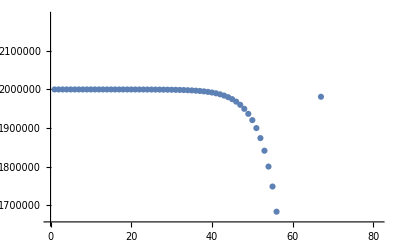

```mathematica
ListPlot[Abs[IndsHarvestedPerYear[[All,1]]-2*10^6]]
```

```mathematica
Abs[IndsHarvestedPerYear[[All,1]]-(2*10^6)]
```

{2.×10^6,2.×10^6,2.×10^6,2.×10^6,2.×10^6,2.×10^6,2.×10^6,1.99999×10^6,1.99999×10^6,1.99999×10^6,1.99999×10^6,1.99999×10^6,1.99998×10^6,1.99998×10^6,1.99997×10^6,1.99997×10^6,1.99996×10^6,1.99995×10^6,1.99994×10^6,1.99992×10^6,1.9999×10^6,1.99987×10^6,1.99984×10^6,1.9998×10^6,1.99975×10^6,1.99968×10^6,1.9996×10^6,1.9995×10^6,1.99937×10^6,1.99921×10^6,1.999×10^6,1.99874×10^6,1.99842×10^6,1.998×10^6,1.99749×10^6,1.99684×10^6,1.99602×10^6,1.99499×10^6,1.99369×10^6,1.99206×10^6,1.99×10^6,1.98741×10^6,1.98415×10^6,1.98005×10^6,1.97488×10^6,1.96838×10^6,1.96019×10^6,1.94988×10^6,1.9369×10^6,1.92057×10^6,1.9×10^6,1.87411×10^6,1.84151×10^6,1.80047×10^6,1.74881×10^6,1.68377×10^6,1.60189×10^6,1.49881×10^6,1.36904×10^6,1.20567×10^6,1.×10^6,741075.,415107.,4737.69,511886.,1.16228×10^6,1.98107×10^6,3.01187×10^6,4.30957×10^6,5.94328×10^6,8.×10^6,1.05893×10^7,1.38489×10^7,1.79526×10^7,2.31189×10^7,2.96228×10^7,3.78107×10^7,4.81187×10^7,6.10957×10^7,7.74328×10^7,9.8×10^7}

```mathematica
HarvestedSize = (2.5)*10^6;
```

```mathematica
HarvestedPosition=Position[Abs[IndsHarvestedPerYear[[All,1]]-HarvestedSize],Min[Abs[IndsHarvestedPerYear[[All,1]]-HarvestedSize]]][[1]][[1]]
```

65

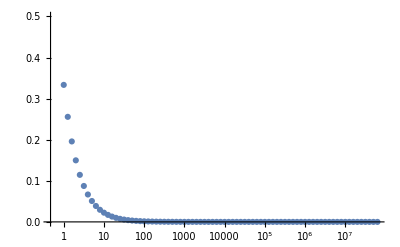

```mathematica
ListLogLinearPlot[Table[{ExtinctionHarvestRate[[i,1]],(SSNoHarvest*(1-fractionremain))/(M*((Log[fractionremain]/(-ξ))*((1/60)*(1/60)*(1/24)*(1/365))))}/.{M->ExtinctionHarvestRate[[i,1]],ξ->ExtinctionHarvestRate[[i,2]]},{i,1,Length[ExtinctionHarvestRate],1}],PlotRange->{0,0.5}]
```

```mathematica
CsolNoPred/.{M->1,ξ->0}
```

0.205291

From Fordham et al. 2021 and Alroy 2001

CC is in grams/m^2 and time is in seconds
Cmax (grams/m^2) = 1.875*10^-6

```mathematica
AlroySol =  DSolve[CC'[t]==-(NN*s*F*CC[t])/(G + CC[t]/(Cmax*M)),CC[t],t]
AlroyTime=Solve[ϵ*Cstart==CC[t]/.AlroySol[[1]],t]/.C[1]->Cstart
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{CC[t]→Cmax G M ProductLog[ⅇ^(-(F NN s t)/G+C[1]/(Cmax G M))/(Cmax G M)]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(Cstart-Cmax G M Log[Cstart ⅇ^((Cstart ϵ)/(Cmax G M)) ϵ])/(Cmax F M NN s)}}

Individuals harvested per meter^2 per second
We can either calculate it from

```mathematica
AlroyHarvestedtoextinction = ((1/M)*(Cstart-ϵ*Cstart))/(t/.AlroyTime[[1]])
```

(Cmax F NN s (Cstart-Cstart ϵ))/(Cstart-Cmax G M Log[Cstart ⅇ^((Cstart ϵ)/(Cmax G M)) ϵ])

Individuals harvested per year in area the size of California

```mathematica
AlroyAnnualharvest=AlroyHarvestedtoextinction*(60*60*24*365)*A
```

(31536000 A Cmax F NN s (Cstart-Cstart ϵ))/(Cstart-Cmax G M Log[Cstart ⅇ^((Cstart ϵ)/(Cmax G M)) ϵ])

Individuals harvested per year in area the size of California

```mathematica
PredictedStart = SSNoHarvest/.{ϵ->0,M->HarvestedSize*2.4}
```

0.724243

```mathematica
annualharvestCA = Flatten[Table[{χF,χN,AlroyAnnualharvest}/.{M->HarvestedSize*2.4,Cmax->1.875*10^-6,G->0.4,NN->1*(1+χN),s->7.884*10^-8,ϵ->fractionremain,A->areaharvested,Cstart->PredictedStart,F->0.35*(1+χF)},{χF,-0.9,0,0.01},{χN,-0.9,0,0.01}],1];
annualharvestTimeCA = Flatten[Table[{χF,χN,(t/.AlroyTime[[1]])*(1/(60*60*24*365))}/.{M->HarvestedSize*2.4,Cmax->1.875*10^-6,G->0.4,NN->1*(1+χN),s->7.884*10^-8,ϵ->fractionremain,A->areaharvested,Cstart->PredictedStart,F->0.35*(1+χF)},{χF,-0.9,0,0.01},{χN,-0.9,0,0.01}],1];
```

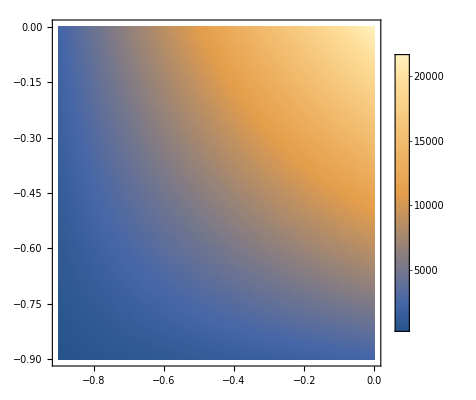

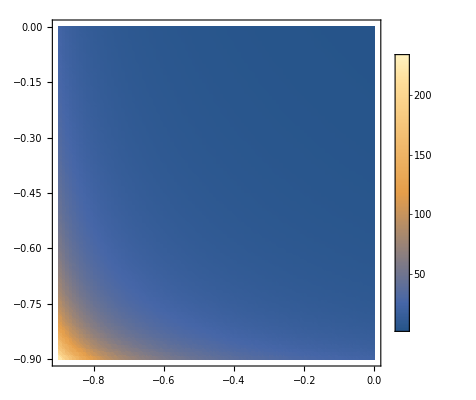

```mathematica
ListDensityPlot[annualharvestCA,PlotLegends->Automatic]
ListDensityPlot[annualharvestTimeCA,PlotLegends->Automatic,PlotRange->All]
```

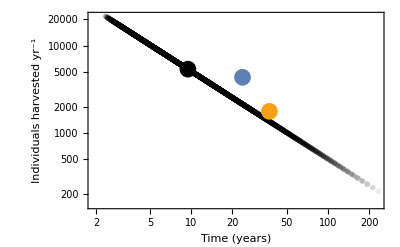

```mathematica
Show[{
ListLogLogPlot[Transpose[{annualharvestTimeCA[[All,3]],annualharvestCA[[All,3]]}],Frame->True,FrameLabel->{"Time (years)","Individuals harvested yr^-1"},LabelStyle->Directive[FontSize->16],PlotRange->All,PlotStyle->Directive[{PointSize[0.01],Opacity[0.08],Black,Point}]],
Graphics[{PointSize[0.03],Black,Point[{Log@(Median[annualharvestTimeCA[[All,3]]]),Log@(Median[annualharvestCA[[All,3]]])}]}],
Graphics[{PointSize[0.03],ColorData[97,1],Point[{Log@IndsHarvestedPerYearTime[[HarvestedPosition,2]],Log@IndsHarvestedPerYear[[HarvestedPosition,2]]}]}],
Graphics[{PointSize[0.03],ColorData[97,13],Point[{Log@IndsHarvestedPerYearTimeWithGenPred[[HarvestedPosition,2]],Log@IndsHarvestedPerYearGenPred[[HarvestedPosition,2]]}]}]
(*,
Graphics[{Thin,Line[{{Log@(2*10^6),Log@Min[Re[annualharvestCA[[All,3]]]]},{Log@(2*10^6),Log@Max[Re[annualharvestCA[[All,3]]]]}}]}]*)
},ImageSize->400]
```

```mathematica
Median[annualharvestTimeCA[[All,3]]]
Median[annualharvestCA[[All,3]]]
```

9.42888

5373.71

```mathematica
(1/λ[M]/.M->HarvestedSize)*(1/(60*60*24*365))
```

3.41975

```mathematica
PredictedStart*(1/(HarvestedSize))
```

2.89697×10^-7

```mathematica
{IndsHarvestedPerYearTime[[HarvestedPosition,2]],IndsHarvestedPerYear[[HarvestedPosition,2]]}
```

{23.6819,4336.6}

```mathematica
IndsHarvestedPerYear
```

{{1.,1.41395×10^11},{1.25893,1.08419×10^11},{1.58489,8.3035×10^10},{1.99526,6.35243×10^10},{2.51189,4.85492×10^10},{3.16228,3.707×10^10},{3.98107,2.8281×10^10},{5.01187,2.15591×10^10},{6.30957,1.64232×10^10},{7.94328,1.25027×10^10},{10.,9.51255×10^9},{12.5893,7.23367×10^9},{15.8489,5.49811×10^9},{19.9526,4.17717×10^9},{25.1189,3.17239×10^9},{31.6228,2.40849×10^9},{39.8107,1.828×10^9},{50.1187,1.38707×10^9},{63.0957,1.05228×10^9},{79.4328,7.9815×10^8},{100.,6.05312×10^8},{125.893,4.59017×10^8},{158.489,3.48055×10^8},{199.526,2.63907×10^8},{251.189,2.00102×10^8},{316.228,1.51727×10^8},{398.107,1.15053×10^8},{501.187,8.72502×10^7},{630.957,6.61736×10^7},{794.328,5.01953×10^7},{1000.,3.80814×10^7},{1258.93,2.88967×10^7},{1584.89,2.1932×10^7},{1995.26,1.665×10^7},{2511.89,1.26436×10^7},{3162.28,9.60404×10^6},{3981.07,7.29759×10^6},{5011.87,5.54699×10^6},{6309.57,4.21793×10^6},{7943.28,3.20861×10^6},{10000.,2.44186×10^6},{12589.3,1.85919×10^6},{15848.9,1.41624×10^6},{19952.6,1.07938×10^6},{25118.9,823092.},{31622.8,628016.},{39810.7,479463.},{50118.7,366283.},{63095.7,280007.},{79432.8,214204.},{100000.,163987.},{125893.,125640.},{158489.,96340.},{199526.,73936.9},{251189.,56795.5},{316228.,43670.4},{398107.,33612.9},{501187.,25899.8},{630957.,19979.7},{794328.,15431.9},{1.×10^6,11935.},{1.25893×10^6,9243.67},{1.58489×10^6,7170.22},{1.99526×10^6,5571.15},{2.51189×10^6,4336.6},{3.16228×10^6,3382.41},{3.98107×10^6,2644.06},{5.01187×10^6,2072.08},{6.30957×10^6,1628.46},{7.94328×10^6,1284.02},{1.×10^7,1016.35},{1.25893×10^7,808.205},{1.58489×10^7,646.369},{1.99526×10^7,520.732},{2.51189×10^7,423.663},{3.16228×10^7,349.634},{3.98107×10^7,295.304},{5.01187×10^7,261.472},{6.30957×10^7,285.322},{7.94328×10^7,171.137-111.54 ⅈ},{1.×10^8,106.46-89.307 ⅈ}}

```mathematica
{{Log@(2*10^6),Min[Re[annualharvestCA[[All,3]]]]},{Log@(2*10^6),Max[Re[annualharvestCA[[All,3]]]]}}
```

{{Log[2000000],216.682},{Log[2000000],21668.2}}

```mathematica
0.1*0.35
```

0.035

```mathematica
Mean[Re[annualharvestCA[[All,3]]]]
```

6554.63

```mathematica
Mean[Re[annualharvestTimeCA[[All,3]]]]
```

15.7061

Bulk estimates of max harvest rate at equilibrium

```mathematica
((1/M)*ExtinctionHarvestRate[[HarvestedPosition,2]]*CsolNoPred/.{M->HarvestedSize,ξ->0})*(60*60*24*365)*areaharvested
```

20252.1

Elephant Trade Calculations

```mathematica
Volume1810=(0.1*1000)*(1*10^3); (*VolumeofTrade in tonnes * 1*10^3 kg per tonne*)
Volume1980 =( 0.95*1000)*(1*10^3);
TuskMass1810=15; (*grams*)
TuskMass1980 = 5;
TusksPerElephant = 1.88;
areaAfrica =3.22122*10^12;(* 3.036*10^13;*) (*meters^2*) (*2.434*10^13*)
areaSubSahAfrica = 2.434*10^13;
ElephantsHarvestedPerYear1810 = Volume1810*1/TuskMass1810*1/TusksPerElephant*areaharvested/areaAfrica
ElephantsHarvestedPerYear1980= Volume1980*1/TuskMass1980*1/TusksPerElephant*areaharvested/areaAfrica
```

466.763

13302.7

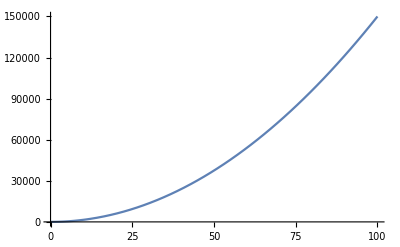

```mathematica
meantuskmass = 5 + 15*Nt^2;
Plot[meantuskmass,{Nt,0,100}]
```

```mathematica
linelegend = LineLegend[{ColorData[97,1],ColorData[97,13],ColorData[97,4]},{"f=0.00","f=0.37","f=1.00"}]
pointlegend = PointLegend[{Black,ColorData[97,3],ColorData[97,18]},{"Mammuthus","Diprotodon","Loxodonta"},LegendMarkerSize->20]
```

```mathematica
linelegendraster = Rasterize[linelegend,RasterSize->500]
pointlegendraster = Rasterize[pointlegend,RasterSize->500]
```

-Graphics-

-Graphics-

```mathematica
Show[linelegend]//Head
```

Show::gtype: LineLegend is not a type of graphics.

Show

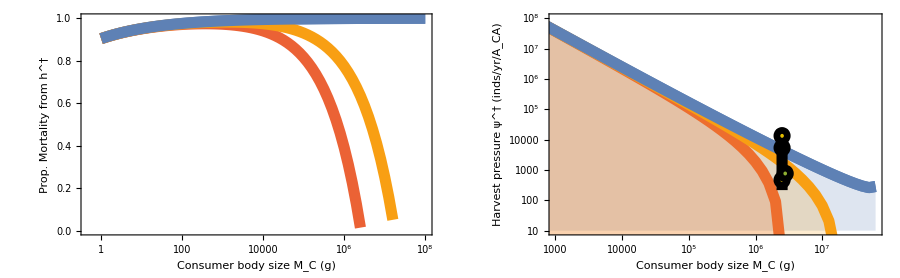

```mathematica
HarvestPlot=GraphicsRow[{
Show[{
ListLogLinearPlot[ExtinctionPercentHarvestMortality,PlotRange->{{All,10^8},{0,1}},Frame->True,FrameLabel->{"Consumer body size M_C (g)","Prop. Mortality from h^†"},LabelStyle->Directive[FontSize->16],PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}],Joined->True(*,Filling->Bottom*)],
ListLogLinearPlot[ExtinctionPercentHarvestMortalityWithPred,Frame->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,4]}],Joined->True(*,Filling->Bottom*)],
ListLogLinearPlot[ExtinctionPercentHarvestMortalityWithGenPred,Frame->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,13]}],Joined->True(*,Filling->Bottom*)],
ListLogLinearPlot[ExtinctionPercentHarvestMortality,Frame->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}],Joined->True(*,Filling->Bottom*)],
Graphics[Inset[linelegendraster,{Log@3,0.2}]]
},ImageSize->800],
Show[{
ListLogLogPlot[IndsHarvestedPerYear,PlotRange->{{1000,All},{10,10^8}},Frame->True,FrameLabel->{"Consumer body size M_C (g)","Harvest pressure ψ^† (inds/yr/A_CA)"},LabelStyle->Directive[FontSize->16],PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}],Joined->True,Filling->Bottom],
ListLogLogPlot[IndsHarvestedPerYearPred,PlotStyle->Directive[{Thickness[0.01],ColorData[97,4]}],Joined->True,Filling->Bottom],
ListLogLogPlot[IndsHarvestedPerYearGenPred,PlotStyle->Directive[{Thickness[0.01],ColorData[97,13]}],Joined->True,Filling->Bottom],
ListLogLogPlot[IndsHarvestedPerYear,PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}],Joined->True,Filling->None],
DiskSize={0.18,0.41};
(*Show[{*)

Graphics[{Thickness[0.01],Black,Line[{{Log@(HarvestedSize),Log@Min[Re[annualharvestCA[[All,3]]]]},{Log@(HarvestedSize),Log@Max[Re[annualharvestCA[[All,3]]]]}}]}],
Graphics[{EdgeForm[{Black,Thickness[0.006],Opacity[1]}],FaceForm[Black],Disk[{Log@(HarvestedSize),Log@(Median[annualharvestCA[[All,3]]])},DiskSize]}],
Graphics[{EdgeForm[{Black,Thickness[0.006],Opacity[1]}],FaceForm[ColorData[97,18]],Disk[{Log@(HarvestedSize),Log@(ElephantsHarvestedPerYear1810)},DiskSize]}],
Graphics[{EdgeForm[{Black,Thickness[0.006],Opacity[1]}],FaceForm[ColorData[97,18]],Disk[{Log@(HarvestedSize),Log@(ElephantsHarvestedPerYear1980)},DiskSize]}],
(*Graphics[{Thick,ColorData[97,3],Line[{{Log@(2.786*10^6),Log@(678.4)},{Log@(2.786*10^6),Log@(848)}}]}],*)
Graphics[{EdgeForm[{Black,Thickness[0.006],Opacity[1]}],FaceForm[ColorData[97,3]],Disk[{Log@(2.786*10^6),Log@(Mean[{678.4,848}])},DiskSize]}],
Graphics[Inset[pointlegendraster,{Log@(10^7),Log@(10^6.5)}]]
(*}]*)
},ImageSize->800]
},Spacings->Scaled[0],ImageSize->900]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2021_TaranWebs/Figures/fig_harvest.pdf"}],HarvestPlot,"PDF"];
```

```mathematica
Median[annualharvestCA[[All,3]]]
```

5373.71

```mathematica
Mean[{678.4,848}]
```

763.2

```mathematica
ElephantsHarvestedPerYear1810
```

466.763

```mathematica
ElephantsHarvestedPerYear1980
```

13302.7